```mathematica
<<FeynCalc`
```

FeynCalc 10.2.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

## ϕϕχ → ϕχ (Higgs Portal, Majorana χ)

```mathematica
(* phi(k1) phi(k2) chi(k3) -> phi(p1) chi(p2) *)
(* Higgs portal: real scalar phi, Majorana fermion chi *)
(* Vertex: phi chi-bar (lams + I lamp gamma5) chi *)
(* 6 diagrams from permutations of 3 external phi momenta *)

FCClearScalarProducts[];

SP[k1,k1]=mY^2;SP[k2,k2]=mY^2;
SP[k3,k3]=mX^2;SP[p1,p1]=mY^2;SP[p2,p2]=mX^2;

SP[k1,k2]=(s12-2 mY^2)/2;
SP[k1,k3]=(s13-mY^2-mX^2)/2;
SP[k1,p1]=mY^2-t1/2;
SP[k2,p1]=mY^2-t2/2;
SP[k3,p1]=(mX^2+mY^2-t3)/2;
SP[k2,k3]=-(s12-2 mY^2)/2-(s13-mY^2-mX^2)/2+(mY^2-t1/2)+(mY^2-t2/2)+(mX^2+mY^2-t3)/2-(3 mY^2)/2;

(* p2=k1+k2+k3-p1 *)
SP[p2,k1]=SP[k1,k1]+SP[k1,k2]+SP[k1,k3]-SP[k1,p1];
SP[p2,k2]=SP[k1,k2]+SP[k2,k2]+SP[k2,k3]-SP[k2,p1];
SP[p2,k3]=SP[k1,k3]+SP[k2,k3]+SP[k3,k3]-SP[k3,p1];
SP[p2,p1]=SP[k1,p1]+SP[k2,p1]+SP[k3,p1]-SP[p1,p1];

(* NR definitions *)
sqrtsNR=2 mY+mX;
sNR=sqrtsNR^2;
EYf=(sNR+mY^2-mX^2)/(2 sqrtsNR);
NRrules={s12->4 mY^2,s13->(mY+mX)^2,t1->2 mY^2-2 mY EYf,t2->2 mY^2-2 mY EYf,t3->mX^2+mY^2-2 mX EYf};

(* Scalar + pseudoscalar vertex *)
vertexS=lams+I lamp GA[5];

(* Amplitudes with propagators inline *)
qFlow={k1,k2,-p1};
ampS[{a_,b_,c_}]:=Module[{qa,qb,P1,P2,d1,d2},
qa=qFlow⟦a⟧;qb=qFlow⟦b⟧;
P1=k3+qa;P2=k3+qa+qb;
d1=ExpandScalarProduct[SP[P1,P1]]-mX^2;
d2=ExpandScalarProduct[SP[P2,P2]]-mX^2;
SpinorUBar[p2,mX].vertexS.(GS[P2]+mX).vertexS.(GS[P1]+mX).vertexS.SpinorU[k3,mX]/(d1 d2)//DiracSimplify];
perms=Permutations[{1,2,3}];
amps=Table[ampS[perms⟦i⟧],{i,1,6}];

(* Process one term: no polarization sums for scalars *)
proc[i_,j_]:=Module[{cc,Mij},
cc=ComplexConjugate[amps⟦j⟧];
Mij=FermionSpinSum[amps⟦i⟧ cc]//Contract//DiracSimplify;
Mij=Mij/.NRrules;
Mij=Mij/.Eps[__]->0;
Mij=PowerExpand[Mij]/.mY->mX/r//FullSimplify];
```

```mathematica
outputDir=FileNameJoin[{NotebookDirectory[],"MsqTerms_YYX_YX_hP_v2"}];
If[!DirectoryQ[outputDir],CreateDirectory[outputDir]];
```

```mathematica
Do[Print["(",i,",",i,") ..."];
term=proc[i,i];
Put[term,FileNameJoin[{outputDir,"diag_"<>ToString[i]<>"_"<>ToString[i]<>".m"}]];
Clear[term];Print["  Done."];,{i,1,6}];

Do[Print["(",i,",",j,") ..."];
term=2 proc[i,j];
Put[term,FileNameJoin[{outputDir,"offdiag_"<>ToString[i]<>"_"<>ToString[j]<>".m"}]];
Clear[term];Print["  Done."];,{i,1,6},{j,i+1,6}];

Print["\nAll 21 terms saved to: ",outputDir];
```

(1,1) ...

Done.

(2,2) ...

Done.

(3,3) ...

Done.

(4,4) ...

Done.

(5,5) ...

Done.

(6,6) ...

Done.

(1,2) ...

Done.

(1,3) ...

Done.

(1,4) ...

Done.

(1,5) ...

Done.

(1,6) ...

Done.

(2,3) ...

Done.

(2,4) ...

Done.

(2,5) ...

Done.

(2,6) ...

Done.

(3,4) ...

Done.

(3,5) ...

Done.

(3,6) ...

Done.

(4,5) ...

Done.

(4,6) ...

Done.

(5,6) ...

Done.

All 21 terms saved to: /home/gab/Desktop/PyCharm_env/secluded_DM/mathematica/MsqTerms_YYX_YX_hP_v2

## Load and sum

```mathematica
outputDir=FileNameJoin[{NotebookDirectory[],"MsqTerms_YYX_YX_hP_v2"}];
files=FileNames["*.m",outputDir];
Print["Loading ",Length[files]," terms..."];
MsqTotal=0;
Do[term=Get[f];MsqTotal+=term;Clear[term];,{f,files}];
MsqAvgNR=MsqTotal/2//Simplify;
```

Loading 21 terms...

```mathematica
MsqAvgNR//FullSimplify
PowerExpand[MsqAvgNR/.{lamp->λ,lams->λ}]//FullSimplify
```

(9 r^3 (lams^6 (1+2 r)^5 (3+2 r)+3 lamp^6 (1-2 r (1+r))^2+lams^4 (lamp+2 lamp r)^2 (9+4 r (4+r (45+4 r (25+2 r (9+2 r)))))+lamp^4 lams^2 (1+2 r) (9+2 r (-5+2 r (40+r (142+r (271+2 r (149+16 r (5+r)))))))))/(mX^2 (2+r) (1+2 r)^4 (-1+r+2 r^2 (2+r))^2)

(72 r^3 (3+r (10+r (70+r (302+r (655+2 r (402+r (281+8 r (13+2 r)))))))) λ^6)/(mX^2 (2+r) (1+2 r)^4 (-1+r+2 r^2 (2+r))^2)

```mathematica
sqrtsNR=2 mY+mX;
sNR=sqrtsNR^2;
Kallen[a_,b_,c_]:=a^2+b^2+c^2-2 a b-2 a c-2 b c;
lambdaNR=Kallen[sNR,mY^2,mX^2]/.mY->mX/r//Simplify;

(* Phase space: Eq.(A11) of 1609.02555 *)
sigmav2NR=MsqAvgNR*Sqrt[lambdaNR]/(64 Pi mY^2 mX sNR);
sigmav2NR=PowerExpand[sigmav2NR]/.mY->mX/r//FullSimplify
```

(9 r^5 √(9+12 r (2+r)) (lams^6 (1+2 r)^5 (3+2 r)+3 lamp^6 (1-2 r (1+r))^2+lams^4 (lamp+2 lamp r)^2 (9+4 r (4+r (45+4 r (25+2 r (9+2 r)))))+lamp^4 lams^2 (1+2 r) (9+2 r (-5+2 r (40+r (142+r (271+2 r (149+16 r (5+r)))))))))/(64 mX^5 π (2+r)^3 (1+2 r)^4 (-1+r+2 r^2 (2+r))^2)

```mathematica
(* For equal couplings lams=lamp=lambda *)
sigmav2Equal=sigmav2NR/.{lams->λ,lamp->λ}//FullSimplify;

(* Delta_HP such that sigmav2 = Delta_HP * lambda^6 / mX^5 *)
DeltaHP=PowerExpand[sigmav2NR*mX^5]//FullSimplify;
DeltaHPEqual=PowerExpand[sigmav2Equal*mX^5/λ^6]//FullSimplify
```

(9 r^5 √(9+12 r (2+r)) (3+r (10+r (70+r (302+r (655+2 r (402+r (281+8 r (13+2 r)))))))))/(8 π (2+r)^3 (1+2 r)^4 (-1+r+2 r^2 (2+r))^2)

```mathematica
Print["\n--- Numerical values of Delta_HP ---"];
Print["r = 1.5: ",N[DeltaHPEqual/. r->3/2]];
Print["r = 2:   ",N[DeltaHPEqual/. r->2]];
Print["r = 3:   ",N[DeltaHPEqual/. r->3]];
Print["r = 5:   ",N[DeltaHPEqual/. r->5]];
Print["r = 10:  ",N[DeltaHPEqual/. r->10]];
Print["r = 20:  ",N[DeltaHPEqual/. r->20]];
Print["r = 100: ",N[DeltaHPEqual/. r->100]];
```

--- Numerical values of Delta_HP ---

r = 1.5: 0.170301

r = 2:   0.29574

r = 3:   0.627188

r = 5:   1.49137

r = 10:  4.14422

r = 20:  10.0294

r = 100: 59.3263

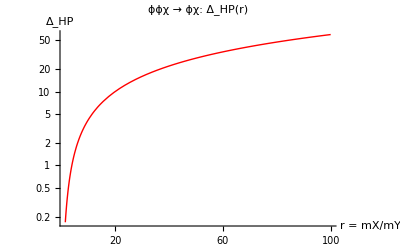

```mathematica
Plot[DeltaHPEqual,{r,1.5,100},
PlotRange->All,
ScalingFunctions->{"Linear","Log"},
AxesLabel->{"r = mX/mY","Δ_HP"},
PlotLabel->"ϕϕχ → ϕχ:  Δ_HP(r)",
PlotStyle->{Thick,Red}]
```